This is the Mathematica notebook associated with the paper “A minimal model of self-organized clusters with phase transitions in ecological communities” by S. Y. Li, M. Kardar, Z. Feng, and W. Taylor. The notebook includes code for simulating the Lotka-Volterra model of self-organized clusters, as well as code for generating the figures.

```mathematica
Needs["MaTeX`"]
```

```mathematica
(*Find a stable, uninvadable fixed point*)
```

```mathematica
FixedPt[S_,k_,α_,λ_:10^-10,t1_:10^6]:=Module[
{network,A,r,n0,sol},
network=RandomGraph[WattsStrogatzGraphDistribution[S,0,k]];
A=Normal[AdjacencyMatrix[network]];
r=ConstantArray[1,S];
n0=RandomReal[{0,1},S];
sol=NDSolve[{n'[t]==n[t] (r-n[t]-α A.n[t])+λ,n[0]==n0},n,{t,0,t1}][[1]];
n[t1]/.sol
]
```

```mathematica
(*Plot of abundances*)
```

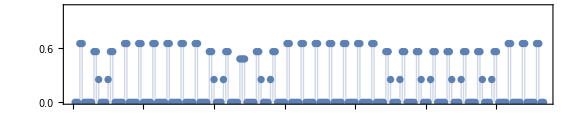

```mathematica
n1=FixedPt[200,4,0.55];
ListPlot[n1,PlotRange->{0,1.05},Filling->Axis,AspectRatio->1/5,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["i",Magnification->1.5],MaTeX["N_i^*",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}]
```

```mathematica
(*Find cluster and gap sizes given a solution n1*)
```

```mathematica
ClusterSizes[n1_,threshold_:10^-5]:=Module[
{positions,rotatedN1},
positions=Flatten@Position[n1,_?(#<threshold&)];
rotatedN1=Append[RotateLeft[n1,positions[[1]]-1],0];
positions=Flatten@Position[rotatedN1,_?(#<threshold&)];
Select[Differences[positions]-1,#>0&]
]
```

```mathematica
GapSizes[n1_,threshold_:10^-5]:=Module[
{positions,rotatedN1},
positions=Flatten@Position[n1,_?(#>threshold&)];
rotatedN1=Append[RotateLeft[n1,positions[[1]]-1],1];
positions=Flatten@Position[rotatedN1,_?(#>threshold&)];
Select[Differences[positions]-1,#>0&]
]
```

## Bifurcation diagram

```mathematica
(*Collect possible steady state abundances for a range of α*)
```

```mathematica
PossibleAbundances[S_,k_,αLow_,αHigh_,αStep_:10^-3,noOfSamples_:10^3]:=Flatten[
ParallelTable[
Table[
Transpose[{ConstantArray[α,S],FixedPt[S,k,α]}]
,{i,noOfSamples}]
,{α,αLow,αHigh,αStep}]
,2];
```

```mathematica
abundances=DeleteDuplicatesBy[PossibleAbundances[100,4,0.497,0.630],Round[#,10^-5]&];
ListPlot[abundances,PlotStyle->PointSize[0.005],PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["\\mathrm{Possible}\\,N_i^*",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}]
```

## Average gap sizes

```mathematica
(*Find average gap sizes from random initial conditions*)
```

```mathematica
AvgGapSizes[S_,k_,αLow_,αHigh_,αStep_:10^-3,noOfSamples_:10^3]:=Module[
{gaps},
ParallelTable[
gaps=Flatten@Table[GapSizes[FixedPt[S,k,α]],{i,noOfSamples}];
If[Length[gaps]==0,0,Mean[gaps]]
,{α,αLow,αHigh,αStep}]
]
```

```mathematica
gaps=AvgGapSizes[100,4,0.30,0.65];
ListPlot[Transpose[{Table[α,{α,0.30,0.65,10^-3}],gaps}],PlotStyle->PointSize[0.005],PlotRange->{0,5},Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["\\alpha",Magnification->1.5],"Average gap size"},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->16}]
```

## Canonical ensemble from random initial conditions

```mathematica
(*This code works for K=1 only*)
```

```mathematica
(*Find the probabilities p(E)/g(E) in canonical ensemble*)
```

```mathematica
LogProbabilities[S_,α_,noOfSamples_:10^4,threshold_:10^-5,roundingError_:10^-4]:=Module[
{trials,n1,lyapunovFn,survivalCount,l,smallClusterCount,largeClusterCount,degeneracy},
trials=ParallelTable[
n1=FixedPt[S,1,α];
lyapunovFn=Round[Total[n1],roundingError];
survivalCount=Count[n1,_?(#>threshold&)];
{lyapunovFn,survivalCount}
,{i,noOfSamples}];
l=Floor[(Pi/ArcCos[1/2/α]-1)/2];
Sort@Table[
largeClusterCount=(2 pattern[[1,2]]-S)/(2 l-1);
smallClusterCount=(S-(2 l+3) largeClusterCount)/2;
degeneracy=S Binomial[largeClusterCount+smallClusterCount,largeClusterCount]/(largeClusterCount+smallClusterCount);
{pattern[[1,1]],Log[pattern[[2]]/noOfSamples/degeneracy]}
,{pattern,Tally[trials]}]
]
```

```mathematica
(*Plot of probabilities*)
```

```mathematica
αList={0.51,0.53,0.55,0.6};
ListLinePlot[
Table[LogProbabilities[200,α],{α,αList}]
,PlotMarkers->Automatic,PlotLegends->Placed[{MaTeX["\\alpha=0.51"],MaTeX["\\alpha=0.53"],MaTeX["\\alpha=0.55"],MaTeX["\\alpha=0.60"]},{Left,Top}],Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["-E^*",Magnification->1.5],MaTeX["\\log [p(E^*)/g(E^*)]",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}
]
```

## Critical points

```mathematica
(*Find the critical point α_c^d given K, d*)
```

```mathematica
CriticalPoint[S_,k_,d_,precision_:10^-3,noOfSamples_:10^3]:=Module[
{αl,αr,αm,gaps},
αl=0;
αr=0.5;
While[αr-αl>precision,
αm=(αl+αr)/2;
gaps=Flatten@ParallelTable[
GapSizes[FixedPt[S,k,αm]]
,{i,noOfSamples}];
If[Max[gaps]>d,αr=αm,αl=αm];
];
αl//N
]
```

```mathematica
(*The critical points for K=15 as an example*)
```

```mathematica
critPts=Table[CriticalPoint[100,15,d],{d,0,14}];
```

```mathematica
γ=Table[Csc[Pi/2/(2 n+1)],{n,Length[critPts],1,-1}]/(1/critPts-1);
```

```mathematica
ListLinePlot[Transpose[{Table[i,{i,0,14}],critPts}],PlotMarkers->Automatic,Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["d",Magnification->1.5],MaTeX["\\alpha_c^d",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}]
```

```mathematica
ListLinePlot[Transpose[{Table[i,{i,0,14}],γ}],PlotRange->{1.9,3.1},PlotMarkers->Automatic,GridLines->{{},{2}},GridLinesStyle->Directive[Black,Dashed,Thick],Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["d",Magnification->1.5],MaTeX["\\gamma(d)",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}]
```

## Number of solutions

This part of code uses data generated from the other Julia program.

```mathematica
(*Read data*)
```

```mathematica
Clear[data];
Do[Get[NotebookDirectory[]<>"data/complete-"<>name<>".m"],{name,{"08","07","06","05","045"}}];
```

```mathematica
alphaList={0.8,0.7,0.6,0.5,0.45};
Show[
(*asymptotics for the first four α*)
Plot[{1.30638^x,1.22074^x,1.19211^x,x^2/12},{x,10,40},ScalingFunctions->"Log"],
(*data points*)
ListPlot[Table[data[α][[All,{1,4}]],{α,alphaList}],ScalingFunctions->"Log",PlotMarkers->Automatic,PlotLegends->Placed[{MaTeX["\\alpha=0.8"],MaTeX["\\alpha=0.7"],MaTeX["\\alpha=0.6"],MaTeX["\\alpha=0.5"],MaTeX["\\alpha=0.45"]},{Left,Top}]],Frame->True,FrameStyle->BlackFrame,FrameLabel->{MaTeX["S",Magnification->1.5],MaTeX["\\mathcal N(K=2,S,\\alpha)",Magnification->1.5]},ImageSize->Large,LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->12}]
```